# Sample waveform for a circular orbit binary without backreaction

## Parameters (mass, initial separation, time before coalescence, distance from detector, and other constants)

```mathematica
G=6.67*^-11;mc=1.21*^30;ι=0;r=(40*^6)*(3.1*^16);tco=17*60;c=3*^8;
```

## The amplitude equation

```mathematica
Φ[t_,mc_]:=-2((5 G mc)/c^3)^(-5/8)t^(5/8);
hp[t_,mc_,r_,ι_,tco_]:=1/r((G mc)/c^2)^(5/4)(5/(c (tco-t)))^(1/4)((1+Cos[ι]^2)/2)Cos[Φ[tco-t,mc]];
hx[t_,mc_,r_,ι_,tco_]:=1/r((G mc)/c^2)^(5/4)(5/(c (tco-t)))^(1/4)Cos[ι]Sin[Φ[tco-t,mc]];
```

## The waveform

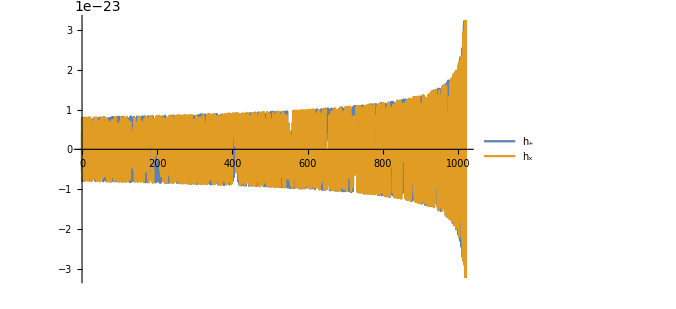

```mathematica
Plot[{hp[t,mc,r,ι,tco],hx[t,mc,r,ι,tco]},{t,0,tco},MaxRecursion->15,PlotPoints->2000,PlotStyle->{Directive[Small],Directive[Small]} ,PlotLegends->{"h_+","h_x"},ImageSize->500]
```

```mathematica
Play[hp[t,mc,r,ι,tco],{t,1010,1019.99}]
Play[hx[t,mc,r,ι,tco],{t,1010,1019.99}]
```

-Graphics-

-Graphics-